# Initialization

```mathematica
$Path=Append[$Path, "C:\\Users\\Dr. Mihaela Bobeica\\Desktop\\Work\\NMR_everything\\SpinDynamica3.4.2\\SDv3.4.2\\SpinDynamica"];
Needs["SpinDynamica`"];
```

# System

## Spin system

```mathematica
SetSpinSystem[2]
```

## Geometry

```mathematica
d=1.7*10^-10;
τc=50*10^-12;
coordinates={{-d/2,0,0},{d/2,0,0}};
ωΣ=0; (*carrier set on average*)
ωΔ=2.8;
J=17.4;
```

```mathematica
Clear[d,τc,coordinates,ωΣ,ωΔ,J]
```

## Hamiltonian

```mathematica
H=2π ωΣ/2(opI[1,"z"]+opI[2,"z"])+2π ωΔ/2(opI[1,"z"]-opI[2,"z"])+π(J*opI[1].opI[2]);
HSL=π(J*opI[1].opI[2])+π*J*opI["x"]+2π ωΣ/2(opI[1,"z"]+opI[2,"z"])+2π ωΔ/2(opI[1,"z"]-opI[2,"z"]);
```

```mathematica
MatrixRepresentation[HSL]//MatrixForm//Simplify
```

(-40.9978 | 0 | 8.79646 | 0
0 | 13.6659 | 38.6531 | 0
8.79646 | 38.6531 | 13.6659 | 38.6531
0 | 0 | 38.6531 | 13.6659)

## Basis set

```mathematica
SetBasis[SingletTripletBasis[]];
SetOperatorBasis[CartesianProductOperatorBasis[]];
```

# Relaxation Superoperator

## Interactions

```mathematica
ω0H = LarmorFrequency[1,4.7];
ωDD=DirectDipolarCoupling[1,d];
ΩDDPR=AxesToEuler[AxisSystem[coordinates⟦1⟧-coordinates⟦2⟧],AxisSystem[-ez]];
```

## DD relaxation

```mathematica
ΓDD=
-6/5*ωDD^2*τc*Sum[(-1)^m *DoubleCommutationSuperoperator[opT[{1,2},{2,-m}],opT[{1,2},{2,m}]],{m,-2,2}];
```

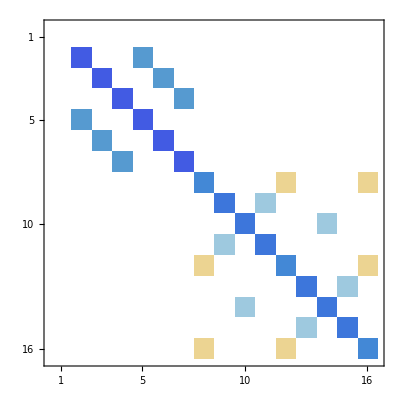

```mathematica
SuperoperatorMatrixRepresentation[ΓDD]//MatrixPlot
```

# Liouvillian

## Liouvillian

```mathematica
Lsop=-ⅈ*CommutationSuperoperator[H]+ΓDD;
LSL=-ⅈ*CommutationSuperoperator[HSL]+ΓDD;
```

# SLIC pulse sequence

```mathematica
slic={RotationSuperoperator[{1,2},{π/2,"y"}],{HSL,τsl},{H,0.4},{HSL,τsl}}/.τsl->0.707/ωΔ;
```

# Singlet Triplet Evolution

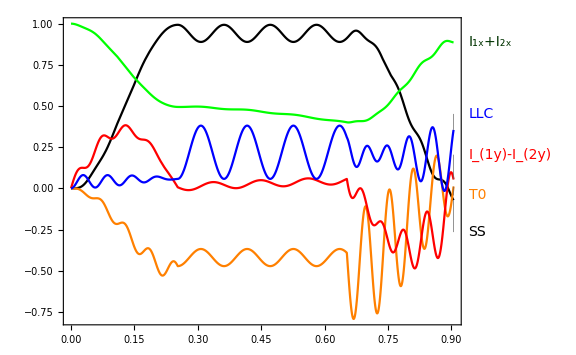

```mathematica
BasisOperators[SingletTripletOperatorBasis[]];
SS=-BasisOperators[SingletTripletOperatorBasis[]][[11]];
T0=-BasisOperators[SingletTripletOperatorBasis[]][[9]];
{trajSS,trajT0,trajX,trajΔY,trajΔZ}=Trajectory[opI["z"]->{SS,T0,opI["x"],opI[1,"y"]-opI[2,"y"],opI[1,"z"]-opI[2,"z"]},slic];
Plot[{trajSS[t],trajT0[t],trajX[t],trajΔY[t],trajΔZ[t]},{t,0,Duration[slic]},PlotRange->All,PlotStyle->{Black, Orange,Green, Red,Blue},PlotLabels->{Style["SS",Black],Style["T0",Orange],Style[opI["x"],Darker[Green,0.8]],Style[opI[1,"y"]-opI[2,"y"],Red],Style["LLC",Blue]},ImageSize->Large]
```